## Extracting info from 1904.07265

## One data set only

### Data

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
PathImp = NotebookDirectory[];
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
data=Import[StringJoin[PathImp,"Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-1*.5/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin[PathImp,"Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-1*.5/2,data2[[i,2]]},{i,40}];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

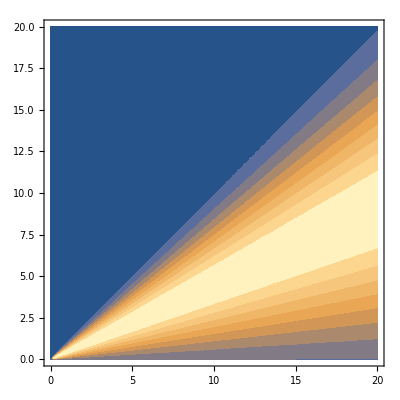

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.}

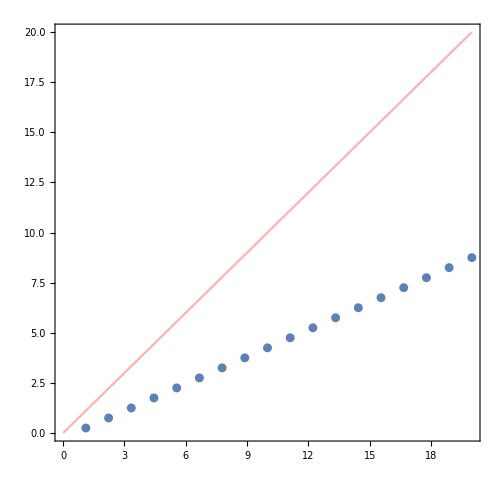

```mathematica
figN=Import["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Mathematica/Img_test_MappingTrueReco.png","Image"];
imageData=ImageData[figN,DataReversed->True];
Manipulate[Graphics[{Raster[imageData,{{0,0},ImageDimensions[figN]}]},ImageSize->500],{{bottomLeft,{0,0}}},{{topRight,{300,300}}},{{bottomLeft,{0,0}},Locator},{{topRight,{300,300}},Locator}];
bottomLeft={42.,51.};
topRight={1.12*755.5,1.08*766.};

{xRange,yRange}={{0,20},{0,20}};

aspectRatio=1/Divide@@(topRight-bottomLeft);
scaling=Abs[Subtract@@xRange]*First@ImageDimensions[figN]/First@(topRight-bottomLeft);


dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,18}]

Show[Plot[x,{x,0,20},{PlotRange->{xRange,yRange},PlotStyle->{{Red,Opacity[0.3]}},Prolog->{Inset[SetAlphaChannel[figN,.5],{xRange[[1]],yRange[[1]]},bottomLeft,scaling]},AxesOrigin->{0.05,1.5},AspectRatio->aspectRatio,Axes->False,ImageSize->500,Axes->True,ImagePadding->50,PlotRangeClipping->False,Frame->True}],ListPlot@Transpose[{dataN,data[[1;;18,1]]}],Frame->True]
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,-8,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[ { data2[[j,1]],Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40} ] },{j,40} ];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)

dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]

dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]

dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
```

54.4842

53.3873

51.3232

1.06159

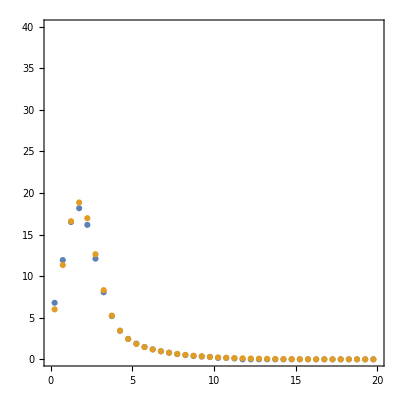

```mathematica
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40} ] },{j,40} ];
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

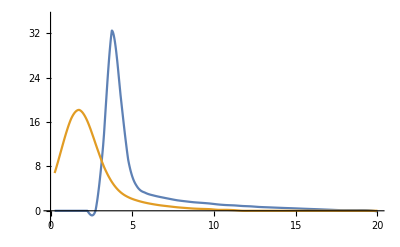

```mathematica
Plot[{dtrue[x],dre[x]},{x,0.25,20},PlotRange->{{0,20},{-2,35}}]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
(* ee is the energy in GeV *)
```

```mathematica
ratio[epS_,ee_]=((0.-2.071438884858977*^-14 ⅈ) epS^2+ee (2.2653175803535897+epS (5.00304469163197+1395.2557007533464 epS))+ee (-2.265317580353589+epS (-19.526840044078167+1355.0510632194855 epS)) Cos[8.323065282815573/ee]+(-0.35192581872734024+epS (-3.159422407231153+256.5539218522311 epS)) Sin[8.323065282815573/ee])/(2.2653175803535897 ee-2.2653175803535897 ee Cos[8.323065282815573/ee]+1.1102230246251565*^-16 ee Cos[16.646130565631147/ee]-0.3519258187273404 Sin[8.323065282815573/ee]);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

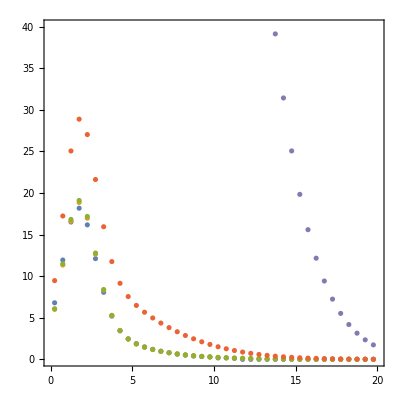

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.00732,6.08311},{11.3392,11.4881},{16.6055,16.8252},{18.8593,19.1049},{16.9728,17.1843},{12.6387,12.7824},{8.31677,8.3955},{5.25726,5.29157},{3.45255,3.46196},{2.44834,2.44518},{1.85978,1.85048},{1.47377,1.46153},{1.19278,1.17928},{0.974477,0.960679},{0.799125,0.785635},{0.655977,0.64318},{0.53818,0.526313},{0.440856,0.43005},{0.360311,0.350623},{0.293644,0.285073},{0.238516,0.231026},{0.193016,0.186542},{0.15556,0.150021},{0.124824,0.120132},{0.0996955,0.0957575},{0.0792373,0.0759615},{0.0626568,0.0599556},{0.0492846,0.0470759},{0.0385555,0.0367645},{0.0299937,0.0285531},{0.0231997,0.0220503},{0.0178398,0.01693},{0.0136364,0.012922},{0.0103601,0.00980347},{0.00782228,0.00739198},{0.00586891,0.0055389},{0.0043751,0.00412398},{0.00324021,0.00305064},{0.00238375,0.00224176},{0.00174178,0.00163629}}

```mathematica
(* checking if it is needed to integrate probability over bin. For nsi = 0.003, nsi2 = nsi*10 and nsi3 = nsi*100 *)
```

```mathematica
Table[
{ NIntegrate[ ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i} ],
ratio[nsi,.5*i]//Chop,
ratio[nsi,.5*i]/NIntegrate[ ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i} ]//Chop }
,{i,40}]//Quiet

Table[
{ NIntegrate[ ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i} ]//Chop,
ratio[nsi2,.5*i]//Chop,
ratio[nsi2,.5*i]/NIntegrate[ ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i} ]//Chop }
,{i,40}]//Quiet

Table[
{ NIntegrate[ ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i} ]//Chop,
ratio[nsi3,.5*i]//Chop,
ratio[nsi3,.5*i]/NIntegrate[ ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i} ]//Chop }
,{i,40}]//Quiet
```

{{0.979537,1.01595,1.03718},{0.946558,1.01416,1.07142},{0.940641,0.995067,1.05786},{1.0106,1.01525,1.00459},{1.01597,1.01631,1.00033},{1.01627,1.01614,0.999869},{1.01588,1.01557,0.999696},{1.01518,1.01477,0.99959},{1.01429,1.01379,0.999506},{1.01324,1.01266,0.999432},{1.01204,1.01139,0.999362},{1.0107,1.00999,0.999295},{1.00923,1.00845,0.999229},{1.00763,1.00679,0.999163},{1.0059,1.005,0.999098},{1.00405,1.00308,0.999033},{1.00206,1.00103,0.998968},{0.999955,0.998858,0.998903},{0.99772,0.99656,0.998838},{0.995358,0.994136,0.998772},{0.992872,0.991587,0.998706},{0.99026,0.988913,0.998639},{0.987523,0.986113,0.998572},{0.984661,0.983189,0.998504},{0.981674,0.980139,0.998436},{0.978563,0.976965,0.998367},{0.975326,0.973666,0.998298},{0.971965,0.970242,0.998228},{0.968478,0.966694,0.998157},{0.964867,0.96302,0.998086},{0.961132,0.959222,0.998013},{0.957271,0.955299,0.99794},{0.953286,0.951252,0.997866},{0.949176,0.94708,0.997791},{0.944942,0.942783,0.997715},{0.940583,0.938362,0.997639},{0.936099,0.933816,0.997561},{0.931491,0.929145,0.997482},{0.926758,0.92435,0.997402},{0.9219,0.91943,0.99732}}

{{-0.10126,1.19451,-11.7964},{8.73052,1.41699,0.162303},{7.65834,3.44895,0.450353},{1.77883,1.28218,0.720801},{1.20567,1.17114,0.971357},{1.17623,1.1915,1.01299},{1.22048,1.2544,1.0278},{1.2964,1.34185,1.03505},{1.3935,1.44802,1.03913},{1.50798,1.57054,1.04149},{1.63816,1.70825,1.04279},{1.7832,1.86054,1.04337},{1.94262,2.02705,1.04346},{2.11615,2.20757,1.0432},{2.30361,2.40194,1.04269},{2.50487,2.61009,1.042},{2.71987,2.83193,1.0412},{2.94855,3.06744,1.04032},{3.19087,3.31657,1.03939},{3.4468,3.57929,1.03844},{3.71631,3.8556,1.03748},{3.9994,4.14546,1.03652},{4.29605,4.44889,1.03558},{4.60624,4.76586,1.03465},{4.92998,5.09636,1.03375},{5.26725,5.4404,1.03287},{5.61805,5.79796,1.03202},{5.98238,6.16905,1.0312},{6.36023,6.55366,1.03041},{6.75159,6.95178,1.02965},{7.15648,7.36343,1.02892},{7.57488,7.78858,1.02821},{8.00679,8.22725,1.02753},{8.45221,8.67943,1.02688},{8.91115,9.14512,1.02626},{9.38359,9.62431,1.02565},{9.86954,10.117,1.02507},{10.369,10.6232,1.02452},{10.882,11.143,1.02398},{11.4084,11.6762,1.02347}}

{{-135.543,6.44436,-0.0475446},{904.799,32.7059,0.0361472},{776.84,275.318,0.354407},{76.0683,16.794,0.220776},{7.64924,3.51552,0.459591},{4.11283,5.92645,1.44097},{9.37644,13.417,1.43092},{18.4215,23.8368,1.29397},{29.9935,36.4923,1.21667},{43.6394,51.0973,1.1709},{59.1585,67.5144,1.14124},{76.4494,85.6699,1.12061},{95.4555,105.521,1.10545},{116.144,127.042,1.09384},{138.492,150.217,1.08466},{162.488,175.032,1.0772},{188.121,201.482,1.07102},{215.386,229.56,1.06581},{244.276,259.262,1.06135},{274.789,290.586,1.05749},{306.922,323.529,1.05411},{340.674,358.089,1.05112},{376.042,394.264,1.04846},{413.025,432.055,1.04607},{451.623,471.46,1.04392},{491.835,512.479,1.04197},{533.66,555.11,1.04019},{577.097,599.353,1.03857},{622.147,645.209,1.03707},{668.808,692.676,1.03569},{717.081,741.755,1.03441},{766.965,792.445,1.03322},{818.461,844.746,1.03211},{871.567,898.657,1.03108},{926.284,954.18,1.03012},{982.612,1011.31,1.02921},{1040.55,1070.06,1.02836},{1100.1,1130.41,1.02755},{1161.26,1192.37,1.0268},{1224.03,1255.95,1.02608}}

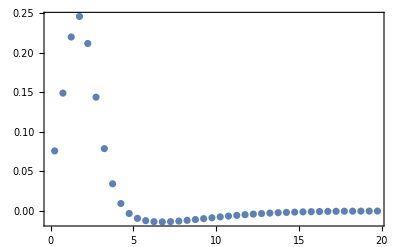

```mathematica
ListPlot[Transpose@{dataT[[All,1]],dataNSI[[All,2]]-dataT[[All,2]]},Frame->True,PlotRange->All]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

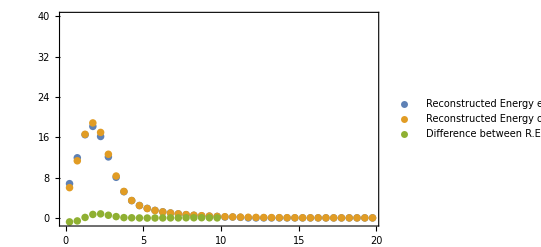

```mathematica
ListPlot[ {data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},
PlotStyle->{PointSize[0.0135],PointSize[0.0135],PointSize[0.0135]},
PlotRange->{All,range} ]
```

The NSI modulus is 0.003

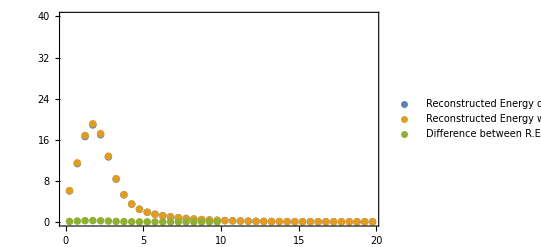

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(dataNSI[[1;;20,2]]-dataT[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},
PlotStyle->{PointSize[0.0135],PointSize[0.0135],PointSize[0.0135]},
PlotRange->{All,range}]
```

The NSI modulus is 0.03

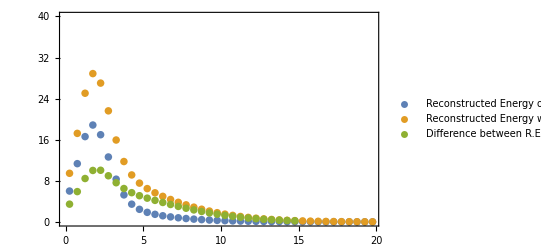

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;30,1]],(dataNSI2[[1;;30,2]]-dataT[[1;;30,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},
PlotStyle->{PointSize[0.0135],PointSize[0.0135],PointSize[0.0135]},
PlotRange->{All,range}]
```

The NSI modulus is 0.3

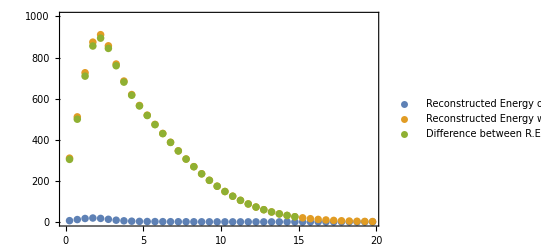

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI3,Transpose[{dataT[[1;;30,1]],(dataNSI3[[1;;30,2]]-dataT[[1;;30,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},

PlotStyle->{PointSize[0.0135],PointSize[0.0135],PointSize[0.0135]},
PlotRange->{All,{0,1000}}]
```

### General Probabilitly ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((-216.76474087618823 ee epS s23 √(1-s23^2)+443.9401382610098 ee epS s23^3 √(1-s23^2)+ee epS (14.523795352446145-17.213387084380614 s23^4) Cos[8.323065282815573/ee-1. δ]-0.555354424129466 ee s23 √(1-s23^2) Cos[δ]+550.8283867001796 ee epS^2 s23^3 √(1-s23^2) Cos[δ]+ee Cos[8.323065282815573/ee] (-8.221113671500182 s23^2+8.221113671500182 s23^4-443.9401382610098 epS √(1-s23^2) (-0.48827470686767177 s23+1. s23^3)+epS^2 (140.54386286655085+5852.64800365708 s23^2-5993.191866523632 s23^4)+550.8283867001796 (0.0010082167831915855+1. epS^2) s23 √(1-s23^2) Cos[δ])+ee epS (2996.595933261816 epS-0.4707740990494358 Cos[8.323065282815573/ee+δ])+39.05849915585865 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-78.1169983117173 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+s23^4 (ee (-8.221113671500182+5993.191866523632 epS^2)+34.42677416876123 ee epS Cos[8.323065282815573/ee+δ]+(1.4466110798466165-1054.5794772081836 epS^2) Sin[8.323065282815573/ee])+s23^2 (ee (8.221113671500182-5852.64800365708 epS^2)+34.42677416876123 ee epS Cos[δ]+(-1.446611079846616+1054.5794772081833 epS^2) Sin[8.323065282815573/ee])-0.5553544241294658 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ])/(2.2653175803535897 ee-2.2653175803535897 ee Cos[8.323065282815573/ee]+1.1102230246251565*^-16 ee Cos[16.646130565631147/ee]-0.3519258187273404 Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passo=.4/10;
dataGen={};dataGenNSI={};dataGenNSI2={};dataGenNSIp={};dataGenNSI2p={};ls23={};
Do[
ss23=(0.582)-.2+passo*i;delta=π;(*-2.5;*)
AppendTo[ls23,ss23];
AppendTo[ dataGen,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40} ] },{j,40} ] ];AppendTo[ dataGenNSI,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi,.5*i],{i,40} ] },{j,40} ] ];AppendTo[ dataGenNSI2,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi2,.5*i],{i,40} ] },{j,40} ] ];AppendTo[ dataGenNSIp,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi,.5*i],{i,40} ] },{j,40} ] ];AppendTo[ dataGenNSI2p,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi2,.5*i],{i,40} ] },{j,40} ] ]
,{i,0,10}];
```

```mathematica
ratioGen[0.582,1*π,0,.5*3]
```

1.00299

0.003

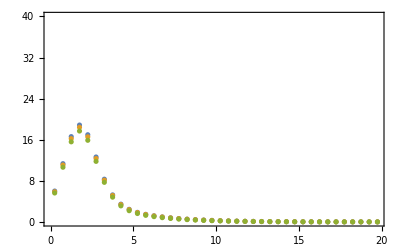
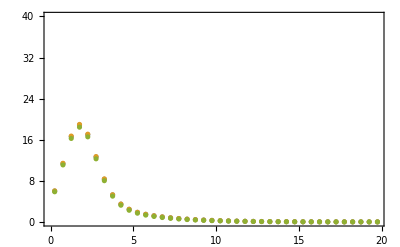
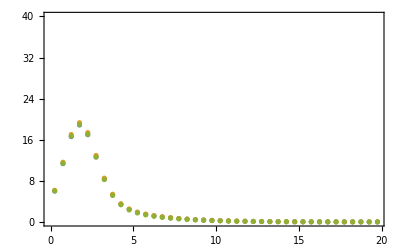
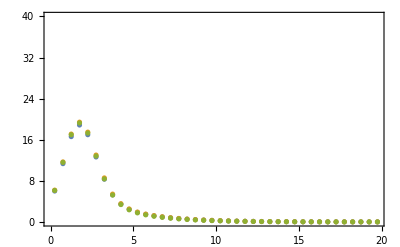
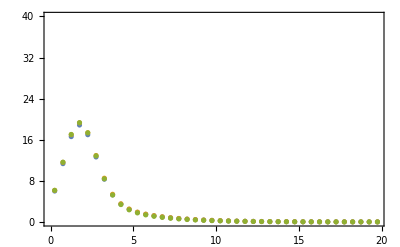
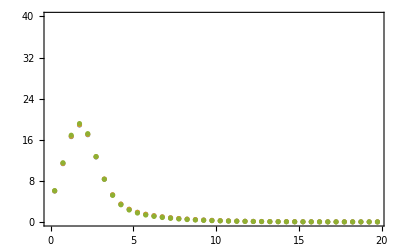
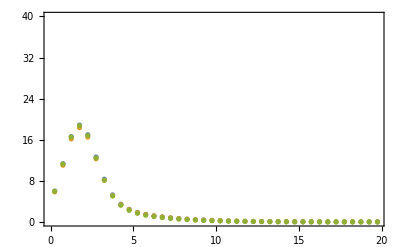
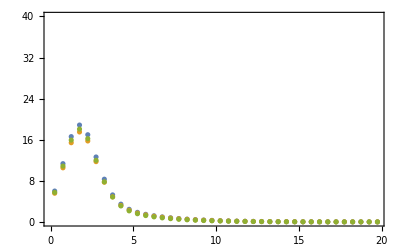

0.03

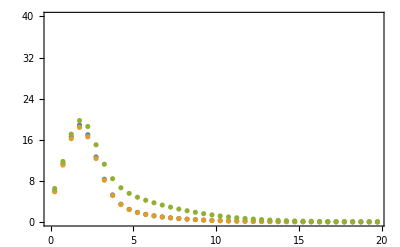
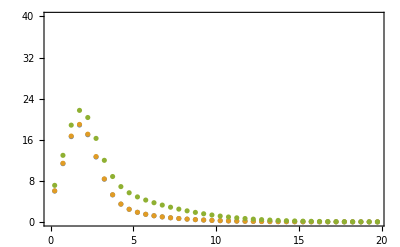
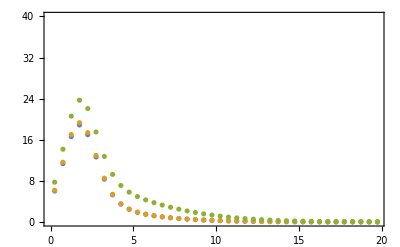
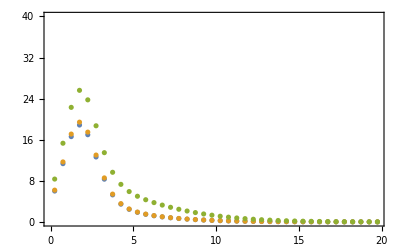
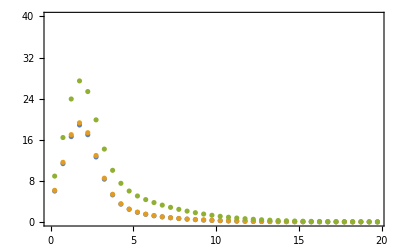
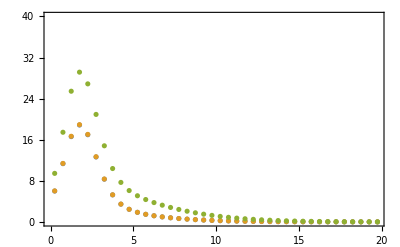
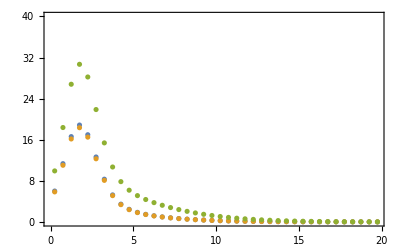
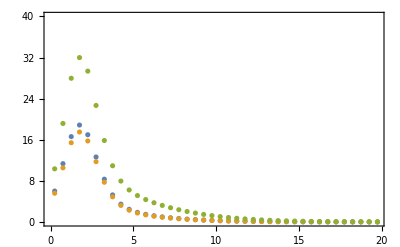

-0.003

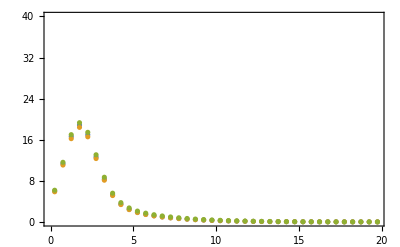
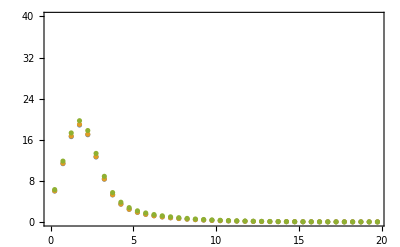
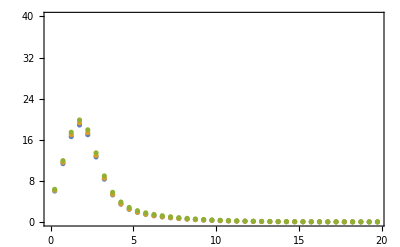
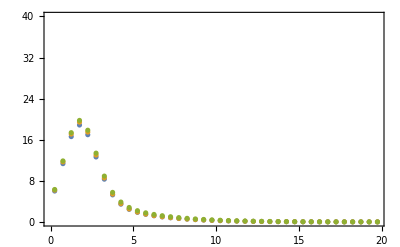
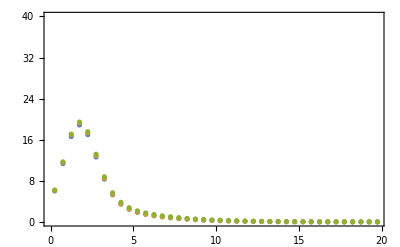
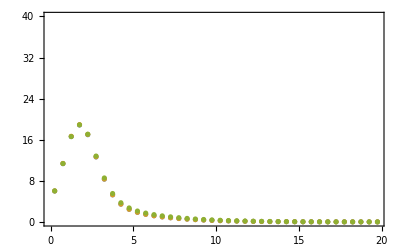
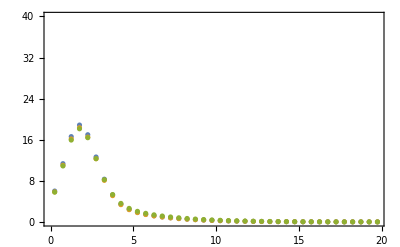
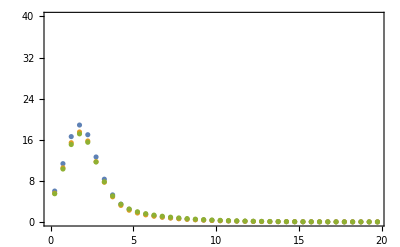

```mathematica
Print[nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[nsi2]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI2[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[-nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSIp[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
```

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.892493,0.92575,1.03726},{0.928089,0.927756,0.999641},{0.930249,0.925118,0.994484},{0.926073,0.926534,1.0005},{0.926707,0.926832,1.00013},{0.926903,0.926961,1.00006},{0.926999,0.927031,1.00003},{0.927054,0.927073,1.00002},{0.927089,0.927102,1.00001},{0.927112,0.927122,1.00001},{0.927129,0.927136,1.00001},{0.927142,0.927147,1.00001},{0.927151,0.927155,1.},{0.927159,0.927162,1.},{0.927164,0.927167,1.},{0.927169,0.927171,1.},{0.927173,0.927175,1.},{0.927176,0.927178,1.},{0.927179,0.92718,1.},{0.927181,0.927182,1.},{0.927183,0.927184,1.},{0.927185,0.927186,1.},{0.927187,0.927187,1.},{0.927188,0.927188,1.},{0.927189,0.927189,1.},{0.92719,0.92719,1.},{0.927191,0.927191,1.},{0.927192,0.927192,1.},{0.927192,0.927193,1.},{0.927193,0.927193,1.},{0.927194,0.927194,1.},{0.927194,0.927194,1.},{0.927195,0.927195,1.},{0.927195,0.927195,1.},{0.927195,0.927196,1.},{0.927196,0.927196,1.},{0.927196,0.927196,1.},{0.927196,0.927197,1.},{0.927197,0.927197,1.},{0.927197,0.927197,1.}}

{{0.472832,0.509968,1.07854},{0.517675,0.516578,0.997882},{0.524793,0.507886,0.967785},{0.511031,0.512552,1.00297},{0.513122,0.513532,1.0008},{0.513769,0.513957,1.00037},{0.514082,0.514188,1.0002},{0.514264,0.514329,1.00013},{0.514379,0.514422,1.00009},{0.514457,0.514488,1.00006},{0.514513,0.514535,1.00004},{0.514554,0.514571,1.00003},{0.514585,0.514598,1.00003},{0.514609,0.51462,1.00002},{0.514629,0.514637,1.00002},{0.514645,0.514651,1.00001},{0.514657,0.514663,1.00001},{0.514668,0.514673,1.00001},{0.514677,0.514681,1.00001},{0.514685,0.514688,1.00001},{0.514691,0.514694,1.00001},{0.514697,0.514699,1.},{0.514702,0.514704,1.},{0.514706,0.514708,1.},{0.51471,0.514711,1.},{0.514713,0.514714,1.},{0.514716,0.514717,1.},{0.514718,0.51472,1.},{0.514721,0.514722,1.},{0.514723,0.514724,1.},{0.514725,0.514726,1.},{0.514727,0.514727,1.},{0.514728,0.514729,1.},{0.51473,0.51473,1.},{0.514731,0.514731,1.},{0.514732,0.514733,1.},{0.514733,0.514734,1.},{0.514734,0.514735,1.},{0.514735,0.514736,1.},{0.514736,0.514736,1.}}

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
(*{0.1298,0.27492,0.40691,0.45459,0.396746,0.25935,0.1190,0.1137,0.464024,1.5124,3.7984}*)
```

```mathematica
chis23=Table[ Sum[ dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[ dataT[[i,2]]/dataGen[[j,i,2]] ],{i,40} ],{j,Length@dataGen} ]//Chop
```

{0.0326437,0.00226081,0.0325266,0.0489447,0.0293249,0.000846823,0.0436655,0.302107,1.00696,2.51689,5.39709}

InterpolatingFunction[…]

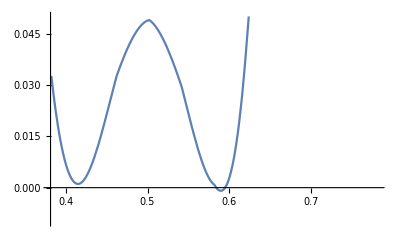

```mathematica
Table[{ls23[[i]],{chis23[[i]]}},{i,Length@ls23}];
Interpolation@%
Plot[%[x],{x,ls23[[1]],ls23[[-1]]},PlotRange->{{0.381,0.782},{-0.01,0.05}}]
```

```mathematica
chiNSI=Table[Sum[dataGenNSI[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.22266,0.181986,0.152555,0.134676,0.128615,0.13467,0.153275,0.185198,0.231943,0.296674,0.386691}

{16.9734,17.468,18.7624,20.9169,23.9763,27.971,32.9179,38.8213,45.6725,53.4482,62.1061}

{0.418046,0.361023,0.317158,0.286427,0.268844,0.264485,0.273539,0.296397,0.333835,0.387353,0.459902}

{87.8503,80.5314,74.3681,69.3649,65.5218,62.838,61.3176,60.9817,61.8921,64.1987,68.2326}

```mathematica
chis23NSI=Table[Sum[dataGenNSI[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.402535,0.152175,0.0883383,0.0943804,0.110878,0.131067,0.203519,0.443158,1.05465,2.37787,4.97881}

{16.2886,17.6946,19.7925,22.3854,25.2643,28.2142,31.0168,33.4493,35.2826,36.2773,36.1776}

{0.262487,0.406228,0.488035,0.476388,0.386066,0.2769,0.258225,0.50007,1.25414,2.8914,5.97088}

{85.5034,81.1188,76.4667,71.7727,67.2524,63.1098,59.534,56.6911,54.7116,53.6716,53.5717}

```mathematica
Join[
Table[{ls23[[i]],nsi,{chis23NSI[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi2,{chis23NSI2[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi,{chis23NSIp[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi2,{chis23NSI2p[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi*0,{chis23[[i]]}},{i,Length@ls23}]
]
func=Interpolation@%
```

{{0.382,0.003,{0.402535}},{0.422,0.003,{0.152175}},{0.462,0.003,{0.0883383}},{0.502,0.003,{0.0943804}},{0.542,0.003,{0.110878}},{0.582,0.003,{0.131067}},{0.622,0.003,{0.203519}},{0.662,0.003,{0.443158}},{0.702,0.003,{1.05465}},{0.742,0.003,{2.37787}},{0.782,0.003,{4.97881}},{0.382,0.03,{16.2886}},{0.422,0.03,{17.6946}},{0.462,0.03,{19.7925}},{0.502,0.03,{22.3854}},{0.542,0.03,{25.2643}},{0.582,0.03,{28.2142}},{0.622,0.03,{31.0168}},{0.662,0.03,{33.4493}},{0.702,0.03,{35.2826}},{0.742,0.03,{36.2773}},{0.782,0.03,{36.1776}},{0.382,-0.003,{0.262487}},{0.422,-0.003,{0.406228}},{0.462,-0.003,{0.488035}},{0.502,-0.003,{0.476388}},{0.542,-0.003,{0.386066}},{0.582,-0.003,{0.2769}},{0.622,-0.003,{0.258225}},{0.662,-0.003,{0.50007}},{0.702,-0.003,{1.25414}},{0.742,-0.003,{2.8914}},{0.782,-0.003,{5.97088}},{0.382,-0.03,{85.5034}},{0.422,-0.03,{81.1188}},{0.462,-0.03,{76.4667}},{0.502,-0.03,{71.7727}},{0.542,-0.03,{67.2524}},{0.582,-0.03,{63.1098}},{0.622,-0.03,{59.534}},{0.662,-0.03,{56.6911}},{0.702,-0.03,{54.7116}},{0.742,-0.03,{53.6716}},{0.782,-0.03,{53.5717}},{0.382,0.,{0.0326437}},{0.422,0.,{0.00226081}},{0.462,0.,{0.0325266}},{0.502,0.,{0.0489447}},{0.542,0.,{0.0293249}},{0.582,0.,{0.000846823}},{0.622,0.,{0.0436655}},{0.662,0.,{0.302107}},{0.702,0.,{1.00696}},{0.742,0.,{2.51689}},{0.782,0.,{5.39709}}}

InterpolatingFunction[…]

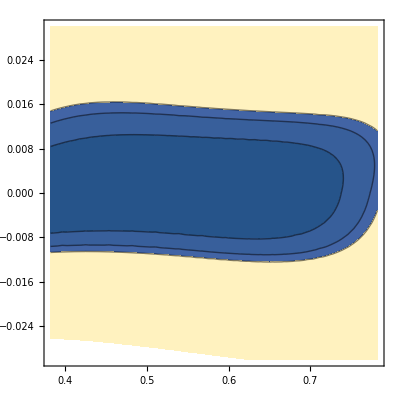

```mathematica
ContourPlot[ func[s23,nsii],{s23,ls23[[1]],ls23[[-1]]},{nsii,-.03,.03},Contours->{2.3,4.6,6.} ]
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {s23,δ} = {Sqrt@0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[
ss23=(Sqrt@0.582)-.2+passos23*i;
Do[
	delta=-2.5-1.+passodelta*k;
	AppendTo[ls23d,{ss23,delta}];
	AppendTo[ dataGen,Table[ { data2[[j,1]],fac2*Sum[ fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i], {i,40} ] },{j,40} ] ]
,{k,0,10}]

,{i,0,10}]//Quiet;
```

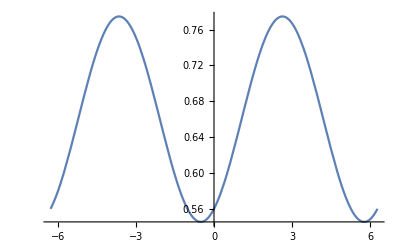

```mathematica
Plot[ratioGen[(Sqrt@0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
ls23d
```

{{0.562889,-3.5},{0.562889,-3.3},{0.562889,-3.1},{0.562889,-2.9},{0.562889,-2.7},{0.562889,-2.5},{0.562889,-2.3},{0.562889,-2.1},{0.562889,-1.9},{0.562889,-1.7},{0.562889,-1.5},{0.602889,-3.5},{0.602889,-3.3},{0.602889,-3.1},{0.602889,-2.9},{0.602889,-2.7},{0.602889,-2.5},{0.602889,-2.3},{0.602889,-2.1},{0.602889,-1.9},{0.602889,-1.7},{0.602889,-1.5},{0.642889,-3.5},{0.642889,-3.3},{0.642889,-3.1},{0.642889,-2.9},{0.642889,-2.7},{0.642889,-2.5},{0.642889,-2.3},{0.642889,-2.1},{0.642889,-1.9},{0.642889,-1.7},{0.642889,-1.5},{0.682889,-3.5},{0.682889,-3.3},{0.682889,-3.1},{0.682889,-2.9},{0.682889,-2.7},{0.682889,-2.5},{0.682889,-2.3},{0.682889,-2.1},{0.682889,-1.9},{0.682889,-1.7},{0.682889,-1.5},{0.722889,-3.5},{0.722889,-3.3},{0.722889,-3.1},{0.722889,-2.9},{0.722889,-2.7},{0.722889,-2.5},{0.722889,-2.3},{0.722889,-2.1},{0.722889,-1.9},{0.722889,-1.7},{0.722889,-1.5},{0.762889,-3.5},{0.762889,-3.3},{0.762889,-3.1},{0.762889,-2.9},{0.762889,-2.7},{0.762889,-2.5},{0.762889,-2.3},{0.762889,-2.1},{0.762889,-1.9},{0.762889,-1.7},{0.762889,-1.5},{0.802889,-3.5},{0.802889,-3.3},{0.802889,-3.1},{0.802889,-2.9},{0.802889,-2.7},{0.802889,-2.5},{0.802889,-2.3},{0.802889,-2.1},{0.802889,-1.9},{0.802889,-1.7},{0.802889,-1.5},{0.842889,-3.5},{0.842889,-3.3},{0.842889,-3.1},{0.842889,-2.9},{0.842889,-2.7},{0.842889,-2.5},{0.842889,-2.3},{0.842889,-2.1},{0.842889,-1.9},{0.842889,-1.7},{0.842889,-1.5},{0.882889,-3.5},{0.882889,-3.3},{0.882889,-3.1},{0.882889,-2.9},{0.882889,-2.7},{0.882889,-2.5},{0.882889,-2.3},{0.882889,-2.1},{0.882889,-1.9},{0.882889,-1.7},{0.882889,-1.5},{0.922889,-3.5},{0.922889,-3.3},{0.922889,-3.1},{0.922889,-2.9},{0.922889,-2.7},{0.922889,-2.5},{0.922889,-2.3},{0.922889,-2.1},{0.922889,-1.9},{0.922889,-1.7},{0.922889,-1.5},{0.962889,-3.5},{0.962889,-3.3},{0.962889,-3.1},{0.962889,-2.9},{0.962889,-2.7},{0.962889,-2.5},{0.962889,-2.3},{0.962889,-2.1},{0.962889,-1.9},{0.962889,-1.7},{0.962889,-1.5}}

```mathematica
dataGen//Dimensions
```

{121,40,2}

7

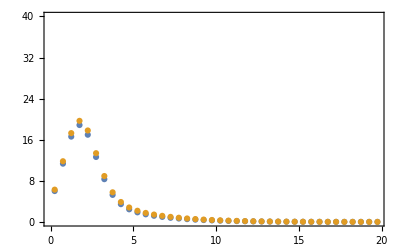

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.127101,0.0104402,0.0223736,0.111313,0.227388,0.329404,0.389867,0.397916,0.36013,0.299257,0.250983,0.279822,0.0692805,0.0023709,0.0292676,0.101405,0.178471,0.233435,0.255486,0.250826,0.241402,0.261652,0.653943,0.299544,0.111961,0.0439883,0.0489964,0.0879755,0.134581,0.178065,0.224069,0.293333,0.418431,1.44561,0.891098,0.535947,0.336424,0.248459,0.234759,0.269873,0.343128,0.459402,0.637818,0.908445,2.96195,2.14111,1.56348,1.18964,0.978696,0.895439,0.915511,1.0283,1.23773,1.56085,2.02457,5.6823,4.51299,3.64526,3.04477,2.67428,2.50101,2.50185,2.66622,2.99682,3.50824,4.22355,10.3782,8.75201,7.5057,6.61055,6.0333,5.7438,5.72022,5.95192,6.44017,7.19664,8.2399,18.3727,16.1341,14.3839,13.0987,12.249,11.8071,11.7522,12.0736,12.7707,13.8521,15.3312,32.1842,29.0837,26.6315,24.8072,23.5834,22.9338,22.8378,23.2841,24.2703,25.8017,27.8868,57.5471,53.1034,49.5757,46.9363,45.1531,44.1961,44.043,44.6804,46.1046,48.319,51.3298,113.224,106.097,100.494,96.3229,93.5096,91.9991,91.755,92.759,95.0095,98.5184,103.307}

InterpolatingFunction[…]

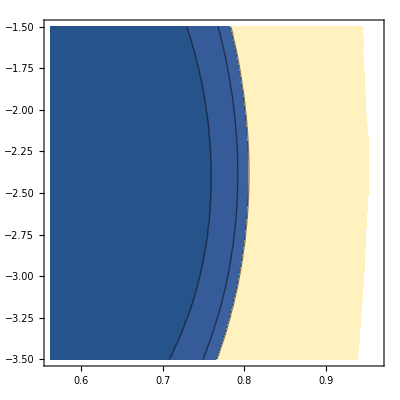

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

### Check probability

```mathematica
ratioGen[S23,dcp,0,ee]
Table[ratioGen[0.582,π,0,ee],{ee,1,10}]
```

(0.-0.555354 ee √(1-S23) √S23 Cos[dcp]+ee (0.-8.22111 S23+8.22111 S23^2+0.555354 √(1-S23) √S23 Cos[dcp]) Cos[8.32307/ee]+S23 (0.+8.22111 ee-1.44661 Sin[8.32307/ee])-0.555354 ee √(1-S23) √S23 Sin[dcp] Sin[8.32307/ee]+S23^2 (0.-8.22111 ee+1.44661 Sin[8.32307/ee]))/(2.26532 ee-2.26532 ee Cos[8.32307/ee]+1.11022×10^-16 ee Cos[16.6461/ee]-0.351926 Sin[8.32307/ee])

{1.0042,1.00364,1.00383,1.00388,1.00391,1.00392,1.00393,1.00393,1.00393,1.00393}

## All data sets - s23 and dm31

```mathematica
(*PathImp = NotebookDirectory[];
data=Import[PathImp,"Mat_WS_In_ModeNu_Tau_minus.txt"];*)
```